## APT Solution to Stefan problem

This represent the analytical solution of the Stefan problem in one dimension. The parameters are approximation to properties of water.

```mathematica
ci = 1.90;
cw = 4.19;
λ = 306;
ki = 0.023;
kw = 0.0058;
v = -5 10^-5;
B= -594;
di := ki/ci; dw= kw/cw; 
α := v/dw; β = v/di;
```

```mathematica
s[t_]:= 15 + v t;
H[x_,t_]:= Piecewise[{{-B + (B+λ) Exp[α( v t-x +15)], x ≤ s[t]},
{-B + B  Exp[β (v t -x +15)],x > s[t]}}];
u[x_,t_]:= Piecewise[{{(H[x,t]-λ)/cw, x ≤ s[t]},
{H[x,t]/ci, x> s[t]}}];
```

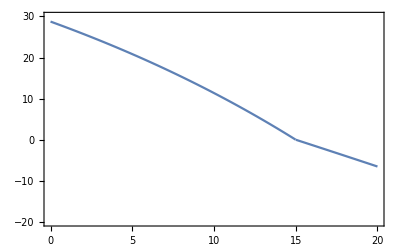

```mathematica
Plot[u[x,0], {x,0,20}, PlotRange->{-20,30}, Frame->True]
```

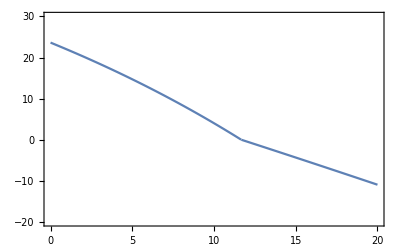

```mathematica
T=200000;
Plot[u[x,T/3], {x,0,20}, PlotRange->{-20,30}, Frame->True]
```

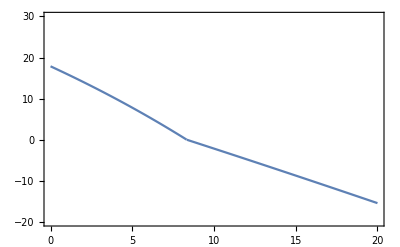

```mathematica
Plot[u[x,2 T/3], {x,0,20}, PlotRange->{-20,30}, Frame->True]
```

Error of the temperature and interface location can be bounded by:

```mathematica
E1[c_,Δt_]:= c (Δt Log[1+T/Δt])^(1/2);
c=100;
```

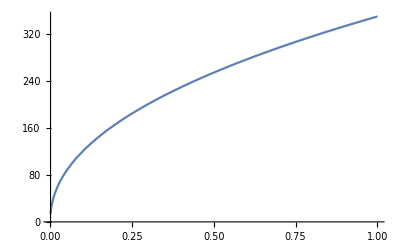

```mathematica
Plot[E1[c,Δt],{Δt,10^-3,1}]
```

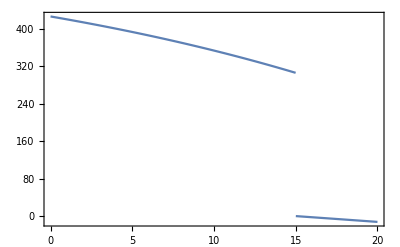

```mathematica
Plot[H[x,0], {x,0,20}, PlotRange->All, Frame->True]
```

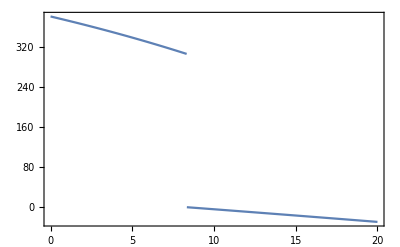

```mathematica
Plot[H[x,2T/3], {x,0,20}, PlotRange->All, Frame->True]
```

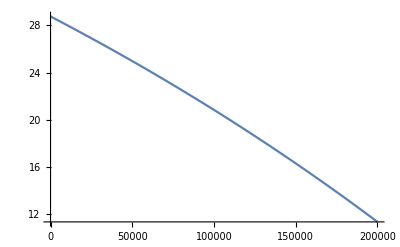

```mathematica
Plot[u[0,t],{t,0,200000}]
```

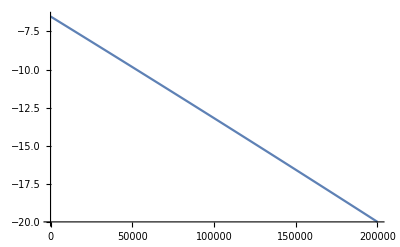

```mathematica
Plot[u[20,t],{t,0,200000}]
```

```mathematica
u[0,t] //Simplify
```

Piecewise[{{312.632-293.85 ⅇ^(2.06522×10^-7 t), t>300000}, {68.7351-39.9828 ⅇ^(1.80603×10^-6 t), True}}]

```mathematica
u[20,t]//Simplify
```

Piecewise[{{312.632-319.155 ⅇ^(2.06522×10^-7 t), t>-100000}, {68.7351-82.3405 ⅇ^(1.80603×10^-6 t), True}}]